```mathematica
(* ******** CODE FOR GENERATING THE LEFT PANELS FROM FIG. 8 ********  *)
```

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

```mathematica
Clear["Global`*"]
```

```mathematica
(* INITIALISATION *)

ui=0.5;
uini = 0.5;
kini = 1;
kmax = 4;
```

```mathematica
(**** PROTOCOLS ****)
```

```mathematica
(* [A - B - A] *)

tfABA[x_,y_]:=Piecewise[{{tf/.NSolve[{1/(x+y)==(1/(kini+uini)+2*(tf-t2))*u^2+2*(t2),1/(x-y)==1/(kini-uini)+2*(tf),1/x==(1/kini+2*(tf-t2))*u+2*(t2),u>0,u<1,tf>0,t2>0},{tf,t2,u}][[1]],Length[NSolve[{1/(x+y)==(1/(kini+uini)+2*t1)*u^2+2*(t2),1/(x-y)==1/(kini-uini)+2*(t1+t2),1/x==(1/kini+2*t1)*u+2*(t2),u>0,u<1,t1>0,t2>0},{t1,t2,u}]]>0.5},{{},Length[NSolve[{1/(x+y)==(1/(kini+uini)+2*t1)*u^2+2*(t2),1/(x-y)==1/(kini-uini)+2*(t1+t2),1/x==(1/kini+2*t1)*u+2*(t2),u>0,u<1,t1>0,t2>0},{t1,t2,u}]]<0.5}}];
```

```mathematica
(* [B - A - B] *)

tfBAB[x_,y_]:=Piecewise[{{tf/.NSolve[{1/(x+y)==(u^2/(kini+uini)+2*tf)*w^2,1/(x-y)==1/(kini-uini)+2*tf,1/x==(u/kini+2*tf)*w,u>0,w>0,tf>0,u<1,w<1},{u,w,tf}][[1]],Length[NSolve[{1/(x+y)==(u^2/(kini+uini)+2*tf)*w^2,1/(x-y)==1/(kini-uini)+2*tf,1/x==(u/kini+2*tf)*w,u>0,w>0,tf>0,u<1,w<1},{u,w,tf}]]>0.5},{{},Length[NSolve[{1/(x+y)==(u^2/(kini+uini)+2*tf)*w^2,1/(x-y)==1/(kini-uini)+2*tf,1/x==(u/kini+2*tf)*w,u>0,w>0,tf>0,u<1,w<1},{u,w,tf}]]<0.5}}];
```

```mathematica
(* [A - C - A] *)

tfACA[x_,y_]:=Piecewise[{{tf/.NSolve[{1/(x-y)==(1/(kini-uini)+2*(tf-t2))*u^2+2*(t2),1/(x+y)==1/(kini+uini)+2*(tf),1/x==(1/kini+2*(tf-t2))*u+2*(t2),u>0,u<1,tf>0,t2>0},{tf,t2,u}][[1]],Length[NSolve[{1/(x-y)==(1/(kini-uini)+2*t1)*u^2+2*(t2),1/(x+y)==1/(kini+uini)+2*(t1+t2),1/x==(1/kini+2*t1)*u+2*(t2),u>0,u<1,t1>0,t2>0},{t1,t2,u}]]>0.5},{{},Length[NSolve[{1/(x-y)==(1/(kini-uini)+2*t1)*u^2+2*(t2),1/(x+y)==1/(kini+uini)+2*(t1+t2),1/x==(1/kini+2*t1)*u+2*(t2),u>0,u<1,t1>0,t2>0},{t1,t2,u}]]<0.5}}];
```

```mathematica
(* [C - A - C] *)

tfCAC[x_,y_]:=Piecewise[{{tf/.NSolve[{1/(x-y)==(u^2/(kini-uini)+2*tf)*w^2,1/(x+y)==1/(kini+uini)+2*(tf),1/x==(u/kini+2*tf)*w,u>0,u<1,tf>0,w>0,w<1},{tf,w,u}][[1]],Length[NSolve[{1/(x-y)==(u^2/(kini-uini)+2*tf)*w^2,1/(x+y)==1/(kini+uini)+2*(tf),1/x==(u/kini+2*tf)*w,u>0,u<1,tf>0,w>0,w<1},{tf,w,u}]]>0.5},{{},Length[NSolve[{1/(x-y)==(u^2/(kini-uini)+2*tf)*w^2,1/(x+y)==1/(kini+uini)+2*(tf),1/x==(u/kini+2*tf)*w,u>0,u<1,tf>0,w>0,w<1},{tf,w,u}]]<0.5}}];
```

```mathematica
(* [A - C - B] and [A - B - C] *)

tfACB[x_,y_]:=Piecewise[{{tf/.NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==(1/(kini-uini)+2*(tf))*w^2,1/x==(1/kini+2*tf)*u*w,u>0,u<1,w>0,w<1,tf>0},{tf,w,u}][[1]],Length[NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==(1/(kini-uini)+2*(tf))*w^2,1/x==(1/kini+2*tf)*u*w,u>0,u<1,w>0,w<1,tf>0},{tf,w,u}]]>0.5},{{},Length[NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==(1/(kini-uini)+2*(tf))*w^2,1/x==(1/kini+2*tf)*u*w,u>0,u<1,w>0,w<1,tf>0},{tf,w,u}]]<0.5}}];
```

```mathematica
(* [B - A - C] *)

tfBAC[x_,y_]:=Piecewise[{{tf/.NSolve[{1/(x+y)==u^2/(kini+uini)+2*tf,1/(x-y)==(1/(kini-uini)+2*(tf))*w^2,1/x==(u/kini+2*tf)*w,u>0,u<1,w>0,w<1,tf>0},{tf,w,u}][[1]],Length[NSolve[{1/(x+y)==u^2/(kini+uini)+2*tf,1/(x-y)==(1/(kini-uini)+2*(tf))*w^2,1/x==(u/kini+2*tf)*w,u>0,u<1,w>0,w<1,tf>0},{tf,w,u}]]>0.5},{{},Length[NSolve[{1/(x+y)==u^2/(kini+uini)+2*tf,1/(x-y)==(1/(kini-uini)+2*(tf))*w^2,1/x==(u/kini+2*tf)*w,u>0,u<1,w>0,w<1,tf>0},{tf,w,u}]]<0.5}}];
```

```mathematica
(* [B - C - A] and [C - B - A] *)

tfBCA[x_,y_]:=Piecewise[{{tf/.NSolve[{1/(x+y)==u^2/(kini+uini)+2*tf,1/(x-y)==w^2/(kini-uini)+2*tf,1/x==u*w/kini+2*tf,u>0,u<1,w>0,w<1,tf>0},{tf,w,u}][[1]],Length[NSolve[{1/(x+y)==u^2/(kini+uini)+2*tf,1/(x-y)==w^2/(kini-uini)+2*tf,1/x==u*w/kini+2*tf,u>0,u<1,w>0,w<1,tf>0},{tf,w,u}]]>0.5},{{},Length[NSolve[{1/(x+y)==u^2/(kini+uini)+2*tf,1/(x-y)==w^2/(kini-uini)+2*tf,1/x==u*w/kini+2*tf,u>0,u<1,w>0,w<1,tf>0},{tf,w,u}]]<0.5}}];
```

```mathematica
(* [C - A - B] *)

tfCAB[x_,y_]:=Piecewise[{{Min[tf/.NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}][[2]],tf/.NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}][[1]]],Length[NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}]]>1.5},{tf/.NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}][[1]],1.5>Length[NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}]]>0.5},{{},Length[NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}]]<0.5}}];

tfCAB2[x_,y_]:=tf/.NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}][[1]];
tfCAB3[x_,y_]:=tf/.NSolve[{1/(x+y)==(1/(kini+uini)+2*tf)*u^2,1/(x-y)==w^2/(kini-uini)+2*(tf),1/x==(w/kini+2*tf)*u,u>0,u<1,w>0,w<1},{tf,w,u}][[2]];
```

```mathematica
(**** PLOTS ****)
```

```mathematica
trel[x_,y_]:=0.5/(x-Abs[y]);
tdiv[x_,y_]:=(x/y)^2*ui^2/(1-ui^2);
```

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

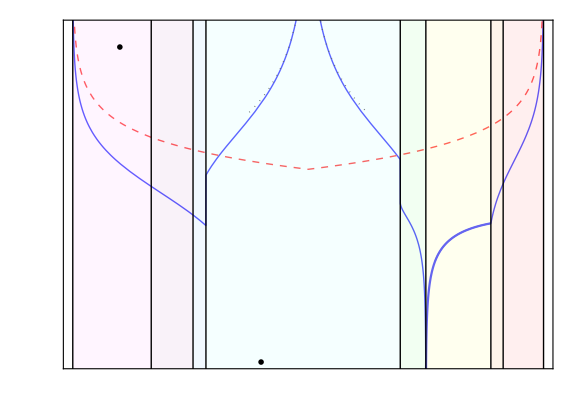

```mathematica
kplot3=2;
Show[LogPlot[Min[Select[{tfACB[kplot3,y],tfBAC[kplot3,y],tfCAB[kplot3,y],tfBAB[kplot3,y],tfABA[kplot3,y],tfACA[kplot3,y],tfCAC[kplot3,y]},UnsameQ[#,{}]&]],{y,-kplot3,kplot3},PlotStyle->{Blue,Thick},PlotRange->All,Filling->{Top,White}],LogPlot[tfCAB3[kplot3,y],{y,-kplot3,0},PlotStyle->Blue,PlotRange->All],LogPlot[tfBAC[kplot3,y],{y,0,kplot3},PlotStyle->Blue,PlotRange->All],LogPlot[3*trel[kplot3,y],{y,-kplot3,kplot3},PlotStyle->{Red,Dashed,Thick},PlotRange->All],LogPlot[tdiv[kplot3,y],{y,-0.5,0.5},PlotStyle->{Black,Dotted,Thick},PlotRange->All],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"u_f","t_f"},Magnification->2],ImageSize->Large,AspectRatio->0.7,Axes->False,FrameTicks->{{Table[{Log[10^i],MaTeX[Superscript[10,i],Magnification->2]},{i,-6,6}],None},{Table[{0.5*i,MaTeX[NumberForm[0.5*i,{2,1}],Magnification->2]},{i,-6,6}],None}},PlotRange->{{-kplot3,kplot3},{Log[0.001],Log[100]}},Epilog->{{LightMagenta,Opacity[0.4],Rectangle[{-2,Log[0.0001]},{-4/3,Log[1000]}]},{LightPurple,Opacity[0.4],Rectangle[{-4/3,Log[0.0001]},{-0.9782,Log[1000]}]},{LightBlue,Opacity[0.4],Rectangle[{-0.9782,Log[0.0001]},{-0.868517,Log[1000]}]},{LightCyan,Opacity[0.4],Rectangle[{-0.868517,Log[0.0001]},{0.7825,Log[1000]}]},{LightGreen,Opacity[0.4],Rectangle[{0.7825,Log[0.0001]},{1,Log[1000]}]},{LightYellow,Opacity[0.4],Rectangle[{1,Log[0.0001]},{1.55247,Log[1000]}]},{LightOrange,Opacity[0.4],Rectangle[{1.55247,Log[0.0001]},{1.65685,Log[1000]}]},{LightRed,Opacity[0.4],Rectangle[{1.65685,Log[0.0001]},{2,Log[1000]}]},{Directive[Black,Thin],{Line[{{-2,Log[0.0001]},{-2,Log[1000]}}],Line[{{-4/3,Log[0.0001]},{-4/3,Log[1000]}}],Line[{{-0.9782,Log[0.0001]},{-0.9782,Log[1000]}}],Line[{{-0.868517,Log[0.0001]},{-0.868517,Log[1000]}}],Line[{{0.7825,Log[0.0001]},{0.7825,Log[1000]}}],Line[{{1,Log[0.0001]},{1,Log[1000]}}],Line[{{1.55247,Log[0.0001]},{1.55247,Log[1000]}}],Line[{{1.65685,Log[0.0001]},{1.65685,Log[1000]}}],Line[{{2,Log[0.0001]},{2,Log[1000]}}]}},Inset[MaTeX["k_f=2",Magnification->1.8],{-1.6,Log[50]},Scaled[{0.125,0.05}]],Inset[MaTeX["1<k_f<k_{\\text{N}^*}",Magnification->1.8],{-0.4,Log[0.001]},Scaled[{0.125,0.05}]]}]
```

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

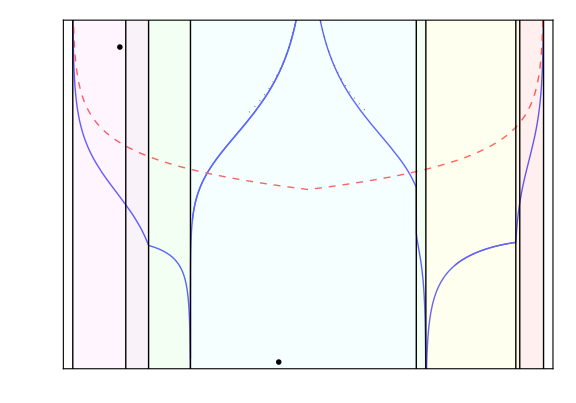

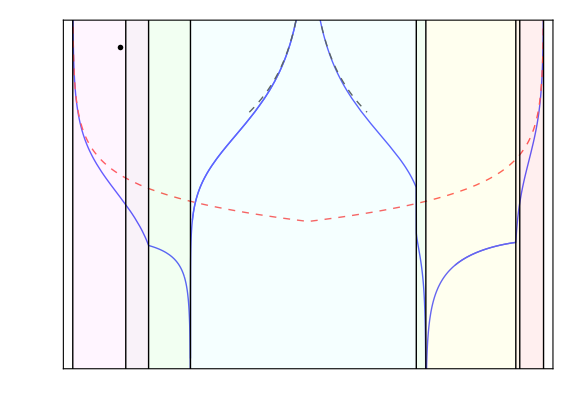

```mathematica
kplot3=4;
Show[LogPlot[Min[Select[{tfACB[kplot3,y],tfBAC[kplot3,y],tfCAB[kplot3,y],tfBAB[kplot3,y],tfABA[kplot3,y],tfACA[kplot3,y],tfCAC[kplot3,y]},UnsameQ[#,{}]&]],{y,-kplot3,kplot3},PlotStyle->{Blue,Thick},PlotRange->All,Filling->{Top,White}],LogPlot[tfCAB3[kplot3,y],{y,-kplot3,0},PlotStyle->{Blue,Thick},PlotRange->All],LogPlot[tfACB[kplot3,y],{y,-kplot3,0},PlotStyle->{Blue,Thick},PlotRange->All],LogPlot[tfBAC[kplot3,y],{y,0,kplot3},PlotStyle->{Blue,Thick},PlotRange->All],LogPlot[3*trel[kplot3,y],{y,-kplot3,kplot3},PlotStyle->{Red,Dashed,Thick},PlotRange->All],LogPlot[tdiv[kplot3,y],{y,-1,1},PlotStyle->{Black,Dotted,Thick},PlotRange->All],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"u_f","t_f"},Magnification->2],ImageSize->Large,AspectRatio->0.7,Axes->False,FrameTicks->{{Table[{Log[10^i],MaTeX[Superscript[10,i],Magnification->2]},{i,-6,6}],None},{Table[{1*i,MaTeX[NumberForm[1*i,{2,1}],Magnification->2]},{i,-6,6}],None}},PlotRange->{{-kplot3,kplot3},{Log[0.001],Log[100]}},Epilog->{{LightMagenta,Opacity[0.4],Rectangle[{-4,Log[0.0001]},{-3.0994,Log[1000]}]},{LightPurple,Opacity[0.4],Rectangle[{-3.0994,Log[0.0001]},{-2.71167,Log[1000]}]},{LightGreen,Opacity[0.4],Rectangle[{-2.71167,Log[0.0001]},{-2,Log[1000]}]},{LightCyan,Opacity[0.4],Rectangle[{-2,Log[0.0001]},{1.8375,Log[1000]}]},{LightGreen,Opacity[0.4],Rectangle[{1.8375,Log[0.0001]},{2,Log[1000]}]},{LightYellow,Opacity[0.4],Rectangle[{2,Log[0.0001]},{3.52872,Log[1000]}]},{LightOrange,Opacity[0.4],Rectangle[{3.52872,Log[0.0001]},{3.5959179,Log[1000]}]},{LightRed,Opacity[0.4],Rectangle[{3.5959179,Log[0.0001]},{4,Log[1000]}]},{Directive[Black,Thin],{Line[{{-4,Log[0.0001]},{-4,Log[1000]}}],Line[{{-3.0994,Log[0.0001]},{-3.0994,Log[1000]}}],Line[{{-2.71167,Log[0.0001]},{-2.7116,Log[1000]}}],Line[{{-2,Log[0.0001]},{-2,Log[1000]}}],Line[{{1.8375,Log[0.0001]},{1.8375,Log[1000]}}],Line[{{2,Log[0.0001]},{2,Log[1000]}}],Line[{{3.52872,Log[0.0001]},{3.52872,Log[1000]}}],Line[{{3.5959179,Log[0.0001]},{3.5959179,Log[1000]}}],Line[{{4,Log[0.0001]},{4,Log[1000]}}]}},Inset[MaTeX["k_f=4",Magnification->1.8],{-3.2,Log[50]},Scaled[{0.125,0.05}]],Inset[MaTeX["k_f>k_{\\text{N}^*}",Magnification->1.8],{-0.5,Log[0.001]},Scaled[{0.125,0.05}]]}]
```

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

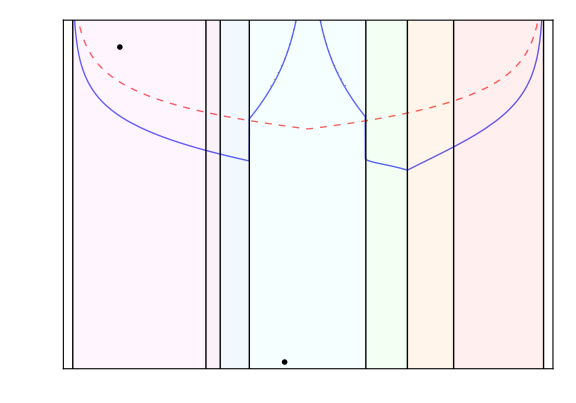

```mathematica
kplot3=0.5;
Show[LogPlot[Min[Select[{tfACB[kplot3,y],tfBAC[kplot3,y],tfCAB[kplot3,y],tfBAB[kplot3,y],tfABA[kplot3,y],tfACA[kplot3,y],tfCAC[kplot3,y]},UnsameQ[#,{}]&]],{y,-kplot3,kplot3},PlotStyle->{Blue,Thick},PlotRange->All,Filling->{Top,White}],LogPlot[tfCAB3[kplot3,y],{y,-kplot3,0},PlotStyle->{Blue,Thick},PlotRange->All],LogPlot[tfBAC[kplot3,y],{y,0,kplot3},PlotStyle->{Blue,Thick},PlotRange->All],LogPlot[3*trel[kplot3,y],{y,-kplot3,kplot3},PlotStyle->{Red,Dashed,Thick},PlotRange->All],LogPlot[tdiv[kplot3,y],{y,-0.08,0.08},PlotStyle->{Black,Dotted,Thick},PlotRange->All],Frame->True,FrameStyle->Directive[Black,28,FontFamily->"Times New Roman"],FrameLabel->MaTeX[{"u_f","t_f"},Magnification->2],ImageSize->Large,AspectRatio->0.7,Axes->False,FrameTicks->{{Table[{Log[10^i],MaTeX[Superscript[10,i],Magnification->2]},{i,-6,6}],None},{Table[{0.25*i,MaTeX[NumberForm[0.25*i,{2,2}],Magnification->2]},{i,-6,6}],None}},PlotRange->{{-kplot3,kplot3},{Log[0.001],Log[100]}},Epilog->{{LightMagenta,Opacity[0.4],Rectangle[{-0.5,Log[0.0001]},{-0.217129,Log[1000]}]},{LightPurple,Opacity[0.4],Rectangle[{-0.217129,Log[0.0001]},{-0.186814,Log[1000]}]},{LightBlue,Opacity[0.4],Rectangle[{-0.186814,Log[0.0001]},{-0.125,Log[1000]}]},{LightCyan,Opacity[0.4],Rectangle[{-0.125,Log[0.0001]},{0.1225,Log[1000]}]},{LightGreen,Opacity[0.4],Rectangle[{0.1225,Log[0.0001]},{0.210768,Log[1000]}]},{LightOrange,Opacity[0.4],Rectangle[{0.210768,Log[0.0001]},{0.30901699,Log[1000]}]},{LightRed,Opacity[0.4],Rectangle[{0.30901699,Log[0.0001]},{0.5,Log[1000]}]},{Directive[Black,Thin],{Line[{{-0.5,Log[0.0001]},{-0.5,Log[1000]}}],Line[{{-0.217129,Log[0.0001]},{-0.217129,Log[1000]}}],Line[{{-0.186814,Log[0.0001]},{-0.186814,Log[1000]}}],Line[{{-0.125,Log[0.0001]},{-0.125,Log[1000]}}],Line[{{0.1225,Log[0.0001]},{0.1225,Log[1000]}}],Line[{{0.210768,Log[0.0001]},{0.210768,Log[1000]}}],Line[{{0.30901699,Log[0.0001]},{0.30901699,Log[1000]}}],Line[{{0.5,Log[0.0001]},{0.5,Log[1000]}}]}},Inset[MaTeX["k_f=0.5",Magnification->1.8],{-0.4,Log[50]},Scaled[{0.125,0.05}]],Inset[MaTeX["k_f<1",Magnification->1.8],{-0.05,Log[0.001]},Scaled[{0.125,0.05}]]}]
```